```mathematica
A1 = 5.457
A2= 1.045*10^-3
A3 = -1.157*10^5
co2= A1 + A2(x) + A3(x)^-2
Integrate[co2,{x,300,450}]
```

5.457

0.001045

-115700.

5.457-115700./x^2+0.001045 x

748.776

```mathematica
Subscript[P, r] = 0.1863
B0 = 0.083-0.422/(T/547.56)^1.6
B1 = 0.139-0.172/(T/547.56)^4.2
Solve[1+(Subscript[P, r]/(T/547.56))(B0+(0.225)*B1)== ((1/44)*(200)*(0.6))/((10.73)*T)]


Z=0.6459
a= (27*1.087)/(64*1.095^2)
b=1.087/(8*1.095)
ξ= a/Z
Solve[Log[ϕ]== Z-1-Log[Z-b]-ξ]
```

0.1863

0.083-10157.9/T^1.6

0.139-(5.45685×10^10)/T^4.2

{{T→-191.739-167.027 ⅈ},{T→-191.739+167.027 ⅈ},{T→62.0418-166.898 ⅈ},{T→62.0418+166.898 ⅈ},{T→248.885}}

0.6459

0.382459

0.124087

0.592134

{{ϕ→0.743945}}

```mathematica
10^8/10^16
```

1/100000000

```mathematica
Simplify[(5!)/(3!*2!)]
```

10

```mathematica
(0.9999)^4
(4*((0.9999)^3*0.0001))+
2*(6*((0.9999)^2*0.0001^2))+
3*4*((0.0001)^3*0.9999)+
4*(0.0001)^4
```

0.9996

0.0004

```mathematica
x=0
y= 1
Binomial[20,x]*(0.04)^x*(0.96)^(20-x)
Binomial[20,y]*(0.04)^y*(0.96)^(20-y)
```

0

1

0.442002

0.368335

```mathematica
Binomial[5,0]
```

1

```mathematica
T= 1.0540
a = 0.152
(1+(0.37464+1.54226*a-0.26992 a^2)(1-Sqrt[T]))^2
```

1.054

0.152

0.968133

```mathematica
Solve[Z^3-Z^2+0.2*Z == 0.01521]
```

{{Z→0.117808-0.0775859 ⅈ},{Z→0.117808+0.0775859 ⅈ},{Z→0.764383}}

```mathematica
8.99*10^9*(2*1.60*10^-19*1.60*10^-19)/((2.05*10^-10)^2)
```

1.09527×10^-8

```mathematica
Solve[-A/r+B/r^n-E== 0, r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-ⅇ-A/r+B r^-n==0,r]

```mathematica
∫(A/nB)^(1/(1-n))ⅆr
```

(A/nB)^(1/(1-n)) r

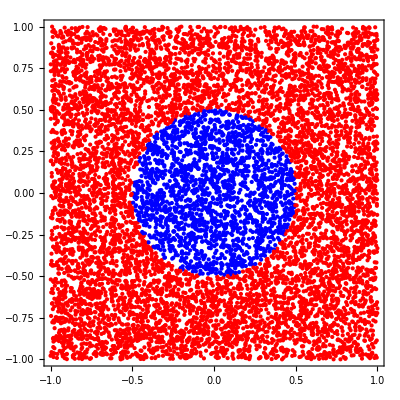

ErrorListPlot[{{4.,1.26491},{3.24,0.36},{3.08,0.110995},{3.1444,0.0354649},{3.1502,0.0112253}}]

```mathematica
pisampleplot[n_] := 
Graphics[Block[{sample,s},Table[sample=RandomReal[{-1,1},2];
If[Norm[sample] ≤ 0.5, s = Blue, s = Red]; 
{s, Point[sample]},{n}]], PlotRange -> {{-1,1},{-1,1}},
AspectRatio -> 1, Frame -> True]
pisampleplot[10000] 
pisample[n_]:= Block[{sample, count=0},
Do [sample = RandomReal[{-1,1},2];
If[Norm[sample]≤ 1, count+= 1], {n}];
4{N[count/n],N[Sqrt[count]/n]}];
ErrorListPlot[Table[pisample[10^l],{l,5.6}]]
```

```mathematica
pisample[n_]:= Block[{sample, count=0},
Do [sample = RandomReal[{-1,1},2];
If[Norm[sample]≤ 1, count+= 1], {n}];
4{N[count/n],N[Sqrt[count]/n]}];
ErrorListPlot[Table[pisample[10^l],{l,5.6}]]
```

ErrorListPlot[{{2.4,0.979796},{3.36,0.366606},{3.084,0.111068},{3.1264,0.0353633},{3.14228,0.0112112}}]

```mathematica
Solve[Log[p/101325]== -((28.85)*(9.81))/8314∫_0^100 1/(300-0.0065z)ⅆz]
Solve[∫_Subscript[p, 1]^Subscript[p, 2] ⅆp/p== -(M*g)/R∫_0^Subscript[z, 2] 1/T[z] ⅆz]
```

{{p→100181.}}

```mathematica
Clear[Z]
A = 0.3921
B = 0.07723

p = -1+B
q =A-2B-3 B^2
r= -A*B + B^2+B^3

Solve[Z^3-0.92277*Z^2+0.219747*Z== 0.0238568]

ξ = A/(Sqrt[8]*B)*Log[(Z+(1+Sqrt[2])*B)/(Z+(1-Sqrt[2])*B)]
Solve[Log[ϕ]== Z-1-Log[Z-B]-ξ]
```

0.3921

0.07723

-0.92277

0.219747

-0.0238568

{{Z→0.143202-0.130316 ⅈ},{Z→0.143202+0.130316 ⅈ},{Z→0.636366}}

```mathematica
Solve[Z^3-Z^2+0.277*Z-0.03185== 0]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {Z→0.143202-0.130316 ⅈ}.

Hold[Solve[Z^3-Z^2+0.277 Z-0.03185==0]]

```mathematica
ω = 0.144
(1+(0.37464+1.54226ω-0.26992 ω^2)*(1-Sqrt[1.095]))^2
```

0.144

0.94587

```mathematica
Z=0.636365720601658
ξ = A/(Sqrt[8]*B)*Log[(Z+(1+Sqrt[2])*B)/(Z+(1-Sqrt[2])*B)]
Solve[Log[ϕ]== Z-1-Log[Z-B]-ξ]
```

0.636366

0.553823

{{ϕ→0.714556}}

```mathematica
DSolve[{(π*(h[t])^2)/(tan[θ])^2*h'[t]== -Sqrt[2*g*h[t]]*a, h[0]== Subscript[H, 0]},h[t],t]
```

{{h[t]→-(((-(1/2))^(1/5) (2 π^2 H_0^5-10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/π^(2/5))},{h[t]→(2 π^2 H_0^5-10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5)/(2^(1/5) π^(2/5))},{h[t]→((-1)^(2/5) (2 π^2 H_0^5-10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/(2^(1/5) π^(2/5))},{h[t]→-(((-1)^(3/5) (2 π^2 H_0^5-10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/(2^(1/5) π^(2/5)))},{h[t]→((-1)^(4/5) (2 π^2 H_0^5-10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/(2^(1/5) π^(2/5))},{h[t]→-(((-(1/2))^(1/5) (2 π^2 H_0^5+10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/π^(2/5))},{h[t]→(2 π^2 H_0^5+10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5)/(2^(1/5) π^(2/5))},{h[t]→((-1)^(2/5) (2 π^2 H_0^5+10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/(2^(1/5) π^(2/5))},{h[t]→-(((-1)^(3/5) (2 π^2 H_0^5+10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/(2^(1/5) π^(2/5)))},{h[t]→((-1)^(4/5) (2 π^2 H_0^5+10 √2 a √g π t H_0^(5/2) tan[θ]^2+25 a^2 g t^2 tan[θ]^4)^(1/5))/(2^(1/5) π^(2/5))}}

```mathematica
Solve[π/(tan[θ])^2∫_((Subscript[Q, 0])^2/(2*g*a))^0 h^(3/2)ⅆh== ∫_0^t -Sqrt[2*g]*aⅆt, t]
```

{{t→(π (Q_0^2/(a g))^(5/2))/(20 a √g tan[θ]^2)}}

```mathematica
Solve[-1000 == (45+Subscript[m, 2])*2766.43-Subscript[m, 2]*(167.54)-137597.85]
```

{{m_2→4.6591}}

```mathematica
x=0.2
0.99-0.2 x^4+0.62 x^3-0.72 x^2+0.42x
```

0.2

1.04984

```mathematica
Subscript[x, a]=0.8
Subscript[x, b]= 0.2
Subscript[x, a] Subscript[x, b](10 Subscript[x, a]+30 Subscript[x, b])
```

0.8

0.2

2.24

```mathematica
Subscript[x, a] Subscript[x, b](10 Subscript[x, a]+30 Subscript[x, b])

Clear["context'^*"]
```

2.24

```mathematica
Simplify[Solve[60 Subscript[y, 1]-40 Subscript[y, 1]^2+30== Subscript[y, 1]*Subscript[V, 1]+(1-Subscript[y, 1])*60, Subscript[V, 1]]]
```

{{V_1→120-30/y_1-40 y_1}}

```mathematica
Subscript[V, M] = Subscript[v, a](1-Subscript[y, b])+80 Subscript[y, b]+2.5(1-Subscript[y, b])Subscript[y, b]
Subscript[V, mix]= Subscript[v, a](1-Subscript[y, b])+80 Subscript[y, b]
Solve[Subscript[v, a](1-Subscript[y, b])+80 Subscript[y, b]==  Subscript[v, a](1-Subscript[y, b])+80 Subscript[y, b]+2.5(1-Subscript[y, b])Subscript[y, b], Subscript[v, a]]
```

{}